### Load MaTeX Styles

```mathematica
<<MaTeX`
```

```mathematica
(*laTex Paths may require adjustment by user*)
ConfigureMaTeX["pdfLaTeX"->"/Library/TeX/texbin/xelatex"];
SetOptions[{MaTeX},"BasePreamble"->{"\\usepackage{mathspec}", "\\usepackage{xcolor}",  "\\usepackage{bm}"}];
text[txt_,size_]:=MaTeX[txt,"Preamble"->{"\\setmainfont{CMU Serif}"},Magnification->size/10];
```

### Import and plot irreversible contour and switching trajectories

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
simulationContourImport =Transpose[ Import["Fig3_Irreversible_SteadyStateDistribution.txt","Table"]];
simulationForward =Import["Fig3_Irreversible_ForwardPath.txt","Table"];
simulationBackward =Import["Fig3_Irreversible_BackwardPath.txt","Table"];
```

```mathematica
simulationContour=DeleteCases[Flatten[Table[If[i+j<Length[simulationContourImport],{j/36,i/36,simulationContourImport[[i+1,j+1]]}],{i,0,Length[simulationContourImport]-1},{j,0,Length[simulationContourImport]-1}],1],Null];
min=Log[10,10^-4];
max=Log[10,10^1];
customLake = ColorDataFunction["LakeColors", "Gradients", {0, 1}, Blend[{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.563821, 0.527565, 0.909499],RGBColor[0.762631, 0.846998, 0.914031],RGBColor[0.941176, 0.906538, 0.834043],RGBColor[1, 1, 1]}, #1] & ];
```

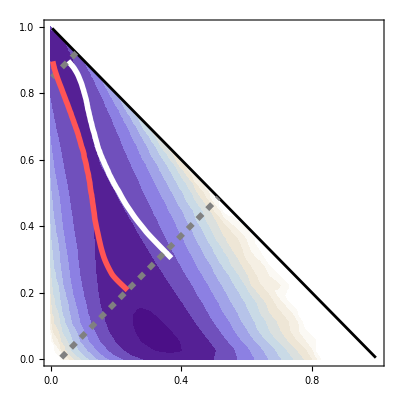

```mathematica
switchingTrajectoryPlotLatticeNonEqLower =Show[ListContourPlot[simulationContour,Contours->Table[10^i,{i,-4,1,.5}],ColorFunction->Function[{f},customLake[1-(Log[10,f]-min)/(max-min)]],ColorFunctionScaling->False,LabelStyle->{20,Black,FontFamily->"CMU Serif"},ContourStyle->None,PlotRange->{10^-5,All},Frame->{{True,False},{True,False}},FrameTicks->{Table[{i,NumberForm[i,{1,1}]},{i,0,1,0.2}],Table[{i,NumberForm[i,{1,1}]},{i,0,1,0.2}]},FrameStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotRangePadding->None,InterpolationOrder->1,FrameLabel->Reverse[Reverse/@{{None,text["N_{1}/N",20]},{None,text["N_{-1}/N",20]}}],ImageSize->Automatic->{450,450},Background->None],

ListLinePlot[simulationForward,PlotStyle->{White,Thickness[0.01]},InterpolationOrder->2]/. Line[x_]:>{Arrowheads[{0,.05,.05,0}],Arrow[x]},


Plot[{1-x,x+(simulationForward[[1]]//Differences),x+(simulationBackward[[1]]//Differences)},{x,0,1},PlotStyle->{{Black,Thickness[0.005]},{Gray,Dashed,Thickness[0.01]},{Gray,Dashed,Thickness[0.01]}},RegionFunction->Function[{x,y},x>0.005&&y>.005&&x+y<1.0001]],

ListLinePlot[simulationBackward,PlotStyle->{Lighter[Red],Thickness[0.01]},InterpolationOrder->2]/. Line[x_]:>{Arrowheads[{0,.05,.05,0}],Arrow[x]}]
```

### Import and plot reversible contour and switching trajectories

```mathematica
simulationContourRevImport =Transpose[ Import["Fig3_Reversible_SteadyStateDistribution.txt","Table"]];
simulationForwardRev =Import["Fig3_Reversible_ForwardPath.txt","Table"];
simulationBackwardRev =Import["Fig3_Reversible_BackwardPath.txt","Table"];
```

```mathematica
simulationContourRev=DeleteCases[Flatten[Table[If[i+j<Length[simulationContourRevImport],{1-i/36,1-j/36,simulationContourRevImport[[i+1,j+1]]}],{i,0,Length[simulationContourRevImport]-1},{j,0,Length[simulationContourRevImport]-1}],1],Null];
```

```mathematica
min=Log[10,10^-4];
max=Log[10,10^1];
customLake = ColorDataFunction["LakeColors", "Gradients", {0, 1}, Blend[{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.563821, 0.527565, 0.909499],RGBColor[0.762631, 0.846998, 0.914031],RGBColor[0.941176, 0.906538, 0.834043],RGBColor[1, 1, 1]}, #1] & ];

legf[x_]:=x/. {NumberForm[y_,{w_,z_}]:>If[Log[10,y]==0,1,("10")^ToString[Round[Log10[y]]]]}
leg = First@Cases[ListContourPlot[simulationContourRev,Contours->Table[10^i,{i,-4,1,.5}],ColorFunction->Function[{f},customLake[1-(Log[10,f]-min)/(max-min)]],ColorFunctionScaling->False,LabelStyle->{20,Black,FontFamily->"CMU Serif"},ContourStyle->None,PlotRange->{10^-5,All},Frame->Reverse/@{{True,False},{True,False}},FrameTicks->{Table[{i,1-i},{i,0,1,0.2}],Table[{i,1-i},{i,0,1,0.2}]},FrameStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotRangePadding->None,InterpolationOrder->1,FrameLabel->{{None,text["N_{1}/N",20]},{None,text["N_{-1}/N",20]}},ImageSize->Automatic->{450,450},PlotLegends->Placed[BarLegend[Table[10^i,{i,-4,1,.5}],LegendFunction->legf,LegendMarkerSize->{50,450},LegendLabel->Placed[Rotate[text["\\text{Steady-State  Probability}",20],3Pi/2],Right]],{1.01,0.43}],Background->None],_BarLegend,All];
```

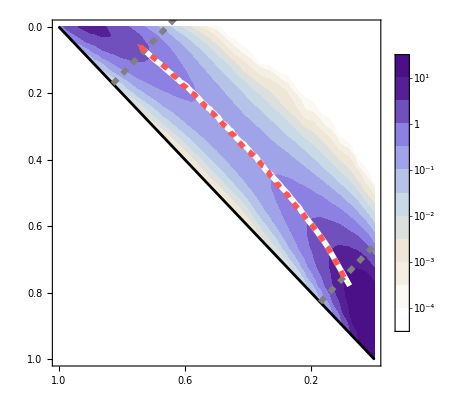

```mathematica
switchingTrajectoryPlotLatticeEq =Legended[ Show[ListContourPlot[simulationContourRev,Contours->Table[10^i,{i,-4,1,.5}],ColorFunction->Function[{f},customLake[1-(Log[10,f]-min)/(max-min)]],ColorFunctionScaling->False,LabelStyle->{20,Black,FontFamily->"CMU Serif"},ContourStyle->None,PlotRange->{10^-5,All},Frame->Reverse/@{{True,False},{True,False}},FrameTicks->{Table[{i,NumberForm[1-i,{1,1}]},{i,0,1,0.2}],Table[{i,NumberForm[1-i,{1,1}]},{i,0,1,0.2}]},FrameStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},PlotRangePadding->None,InterpolationOrder->1,FrameLabel->{{None,text["N_{1}/N",20]},{None,text["N_{-1}/N",20]}},ImageSize->Automatic->{450,450},Background->None],

ListLinePlot[Reverse/@(1-simulationForwardRev),PlotStyle->{White,Thickness[0.01]},InterpolationOrder->2]/. Line[x_]:>{Arrowheads[{0,.05,.05,0}],Arrow[x]},


Plot[{1-x,x+(simulationForwardRev[[1]]//Differences),x+(simulationBackwardRev[[1]]//Differences)},{x,0,1},PlotStyle->{{Black,Thickness[0.005]},{Gray,Dashed,Thickness[0.01]},{Gray,Dashed,Thickness[0.01]}},RegionFunction->Function[{x,y},x+y>0.999]],

ListLinePlot[Reverse/@(1-simulationBackwardRev),PlotStyle->{Lighter[Red],Thickness[0.01],Dashed},InterpolationOrder->2]/.Line[x_]:>{Arrowheads[{0,0,.06,0,0,0,0,0,.06, 0,0,0,0,.06,0}],Arrow[x]}],Placed[leg,Right]]
```

### Combine and label plots

```mathematica
switchingTrajectoryPlotCombinedLattice = Show[switchingTrajectoryPlotLatticeNonEqLower,Epilog->{Inset[switchingTrajectoryPlotLatticeEq,{1,1},{0.35,0.65},450],Text[Column[text[{"\\text{Irreversible}","\\Delta G \\to \\infty"},22],Center],{0.7,0.09}],Text[Column[text[{"\\text{Reversible}","\\Delta G =0"},22],Center],{0.9,0.95}]},PlotRangeClipping->False,ImagePadding->{{Automatic,205},{Automatic,90}}]
```

-Graphics-

### Export

```mathematica
Export["switchingTrajectoryCombined_Lattice.jpg",switchingTrajectoryPlotCombinedLattice,ImageResolution->1000,Background->None];
```